## **************** RG Setup ****************

```mathematica
dim=8;
Clear[μ,η,y]
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x1*x3+y*x0*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0≤1,x0+=2,For[x2=-1,x2≤1,x2+=2,For[x4=-1,x4≤1,x4+=2,leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];]]]
(*Equates the unrenormalized with the renormalized variables*)

req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4]==leq[4];
req[5]==leq[5];
req[6]==leq[6];
req[7]==leq[7];
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0][[1]];
SB[0]={B[0]->2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0&&B[3]>0&&B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0&&B[3]>0&&B[0]>0&&B[2]>0&&B[4]>0&&B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0&&B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0&&B[5]>0&&B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0&&μ>0&&A[0]>0&&A[1]>0&&A[2]>0&&A[3]>0&&A[4]>0&&A[5]>0)],B[5]],1]];
SBT=Table[Part[SB[n],1],{n,0,5}]
```

{B[0]→2 A[0]+Log[(η √μ A[1]^2 A[3] A[5])/(((A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2) (1+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[3]^4 A[5]^2))^(1/8) ((η^2 A[1]^4+2 η μ A[1]^2 A[5]+A[5]^2) (η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)) (A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)))^(1/4))],B[1]→(A[1] A[2] √(η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)) ((A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2)/(A[3]^2 A[5]^2+η^4 A[1]^8 A[3]^2 A[5]^2+η^3 μ A[1]^6 A[5] (1+A[3]^4+2 A[3]^2 A[5]^2)+η μ A[1]^2 A[5] (2 A[3]^2+A[5]^2+A[3]^4 A[5]^2)+η^2 A[1]^4 ((1+A[3]^4) A[5]^2+μ^2 (A[5]^2+A[3]^4 A[5]^2+A[3]^2 (1+A[5]^4)))))^(1/4))/(η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+2 η μ A[1]^2 A[3]^2 A[5] (1+η^2 A[1]^4 A[5]^2)+2 η μ A[1]^2 A[3]^6 A[5] (1+η^2 A[1]^4 A[5]^2)+A[3]^4 (1+4 η^2 μ^2 A[1]^4 A[5]^2+η^4 A[1]^8 A[5]^4))^(1/8),B[2]→((μ^(-1+y) (A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2))/(1+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[3]^4 A[5]^2))^(1/8) ((μ^(1/2-y/2) (A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)))/(η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)))^(1/4),B[3]→(A[3] A[4] √(η^2 A[1]^4+2 η μ A[1]^2 A[5]+A[5]^2))/(η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+2 η μ A[1]^2 A[3]^2 A[5] (1+η^2 A[1]^4 A[5]^2)+2 η μ A[1]^2 A[3]^6 A[5] (1+η^2 A[1]^4 A[5]^2)+A[3]^4 (1+4 η^2 μ^2 A[1]^4 A[5]^2+η^4 A[1]^8 A[5]^4))^(1/4),B[4]→(μ^y (η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)) (A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)))/((η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+2 η μ A[1]^2 A[3]^2 A[5] (1+η^2 A[1]^4 A[5]^2)+2 η μ A[1]^2 A[3]^6 A[5] (1+η^2 A[1]^4 A[5]^2)+A[3]^4 (1+4 η^2 μ^2 A[1]^4 A[5]^2+η^4 A[1]^8 A[5]^4))^(1/4) √((η^2 A[1]^4+2 η μ A[1]^2 A[5]+A[5]^2) (A[3]^2 A[5]^2+η^4 A[1]^8 A[3]^2 A[5]^2+η^3 μ A[1]^6 A[5] (1+A[3]^4+2 A[3]^2 A[5]^2)+η μ A[1]^2 A[5] (2 A[3]^2+A[5]^2+A[3]^4 A[5]^2)+η^2 A[1]^4 ((1+A[3]^4) A[5]^2+μ^2 (A[5]^2+A[3]^4 A[5]^2+A[3]^2 (1+A[5]^4)))))),B[5]→((A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)) √((A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2)/(A[3]^2 A[5]^2+η^4 A[1]^8 A[3]^2 A[5]^2+η^3 μ A[1]^6 A[5] (1+A[3]^4+2 A[3]^2 A[5]^2)+η μ A[1]^2 A[5] (2 A[3]^2+A[5]^2+A[3]^4 A[5]^2)+η^2 A[1]^4 ((1+A[3]^4) A[5]^2+μ^2 (A[5]^2+A[3]^4 A[5]^2+A[3]^2 (1+A[5]^4))))))/(η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+2 η μ A[1]^2 A[3]^2 A[5] (1+η^2 A[1]^4 A[5]^2)+2 η μ A[1]^2 A[3]^6 A[5] (1+η^2 A[1]^4 A[5]^2)+A[3]^4 (1+4 η^2 μ^2 A[1]^4 A[5]^2+η^4 A[1]^8 A[5]^4))^(1/4)}

```mathematica
(* Set up Initial values(SIC),Initial Step, RG steps, W, Z1, LnZ1, DLnZ1, and constants*)
Clear[μ,η,y]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->μ^(y),B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[D[(B[i]/.SBT),A[j]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];];
RGW:=Block[{},Υ=Together[Υ.(W/.SAT)];
RG;];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4 μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
```

```mathematica
SIC
Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
dA0dμ
Table[D[A[i]/.SAT,η],{i,0,dim-1}]
dA0dη
```

{B[0]→0,B[1]→η,B[2]→η,B[3]→μ,B[4]→μ^y,B[5]→1}

{0,0,0,1,y μ^(-1+y),0,1,0}

{0,0,0,-4 μ,-4 y μ^y,0,-4 μ,0}

{0,1,1,0,0,0,0,1}

{0,-2 η,-2 η,0,0,0,0,-2 η}

```mathematica
Tmin=N[0.001,precN];
Tmax=N[12,precN];
Tinc=N[0.5,precN];
Tvector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=Exp[2/Tvector]
```

{3.88118019428×10^868,54.164,7.37431,3.7903,2.71692,2.22483,1.9473,1.77051,1.64852,1.55947,1.49171,1.43846,1.39553,1.36022,1.33066,1.30556,1.28399,1.26525,1.24882,1.2343,1.22138,1.2098,1.19938,1.18993}

```mathematica
(***** AFM One Point Function*****)
```

```mathematica
(***** Constants for IE: Internal Energy*****)
Clear[μ,y,η]
InitRGW;
y=1;
precN=1000;
Tmin=N[0.011,precN];
Tmax=N[12.0,precN];
Tinc=N[0.005,precN];
Tvector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=Exp[2/Tvector];
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};
(*******Internal Energy<e>*******)
Clear[μ,η];
InitRGW;
dμdβ=-4 μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
η=N[1.0,precN];
IE=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[Tvector][[1]]}];
μind=0;
Do[kind=1;
μind++;
μ=N[μVector[[μind]],precN];
InitRGW;
For[i=3,i≤Max[kVector],++i,RGW;
If[i==kVector[[kind]],Part[Part[IE,kind],μind]=1/2^(i)*(dA0dμ.Υ).(DLnZ1/.SAT);kind++,];],{Tx,Tmin,(Tmax+Tinc),Tinc}];
Rasterize[ListLinePlot[Table[Table[{1.0/μVector[[i]],IE[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=24"},PlotStyle->Thick]]
IEc=IE;
PrependTo[IEc,Tvector];
PrependTo[IEc,1.0/μVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
IEc=Transpose[IEc];
IEc=PrependTo[IEc,kVector];
If[y==0,Export["./GoogleDrive/Research/AntiHN/Maca/data/HN3_AFM_IE.csv",IEc],Export["./GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_IE.csv",IEc]]
```

$Aborted

-Graphics-

./GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_IE.csv

```mathematica
Export["./GoogleDrive/ie.csv",Transpose[IEc]]
```

./GoogleDrive/ie.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["ie.csv"]]]
```

```mathematica
Min[IE[[4]]]
```

-1.16667

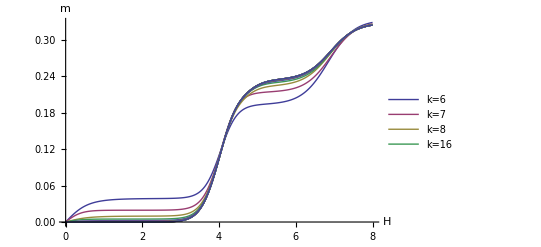

./GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_magH_m5e8.csv

```mathematica
(***** Constants for magnetization: <m> vs H*****)
Clear[μ,η,y];
InitRGW;
μ=5*^8;(*1:high T;1000:low T*)
y=1;
Hmin=0.0;
Hmax=8;
Hinc=0.01;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-Hmin];
ηmin=Exp[-Hmax];
ηVector=Exp[-HVector];
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,128};
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(*Magnetization at different H at μ=0.01*)InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,];];];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=16"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,ηVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
If[y==0,Export["./GoogleDrive/Research/AntiHN/Maca/data/HN3_AFM_magH_m5e8.csv",MagHc],Export["./GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_magH_m5e8.csv",MagHc]]
```

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η,y];
InitRGW;
precN=200;
y=1;
Tmin=N[0.011,precN];
Tmax=N[12.0,precN];
Tinc=N[0.1,precN];
Tvector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=N[Exp[2/Tvector],precN];
kVector={10,12,14,16,32}(*,64,128}*);
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-1/100],precN];
Print["iteration starting..."];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=N[1/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT),20];kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]
ListLogPlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full,Joined->True]
```

iteration starting...

-Graphics-

-Graphics-

```mathematica
μ
```

0.844227

```mathematica
y
```

0

```mathematica
(*********************************Magnetization Plots**************************************)
μinvmin=N[0.01,100];
μinvmax=1;
μinvinc=N[0.01,100];
μVector=1.0/Range[μinvmin,μinvmax,μinvinc];
μinvVector=1.0/μVector;
kVector={8,10,12,16}(*,64,128}*);
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
```

1/ⅇ^(1/1400)=0.99928596932702736552000752952703226511617004974682

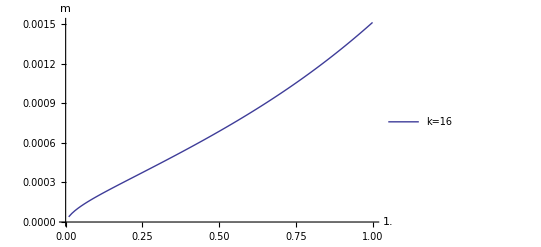

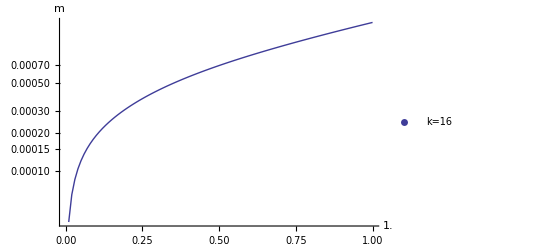

```mathematica
Clear[μ,η,y];
y=0;
InitRGW;
dηdH=-2η;
kind=1;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/1400];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),
];
];
];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=16","k=32","k=64","k=128"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]
ListLogPlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=16","k=32","k=64","k=128"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full,Joined->True]
```

1/ⅇ^(1/20000)=0.99995000124997916692708072918836790054660372725663

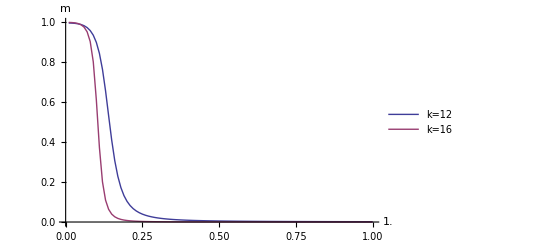

```mathematica
Clear[μ,η,y];
y=0;
InitRGW;
dηdH=-2η;
kind=2;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/20000];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]
```

1/ⅇ^(1/100000000)=0.99999999000000004999999983333333374999999916666667

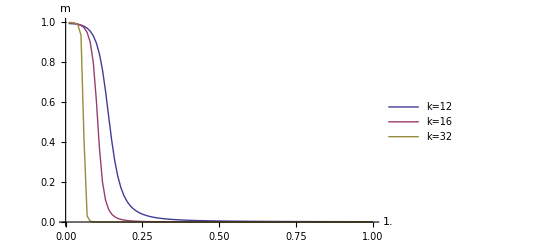

```mathematica
Clear[μ,η,y];
y=0;
InitRGW;
dηdH=-2η;
kind=3;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/10^8];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]
```

1/ⅇ^(1/1000000000000000)=0.99999999999999900000000000000049999999999999983333

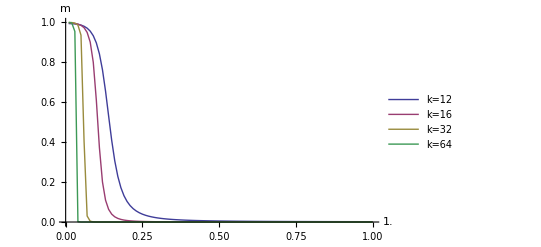

```mathematica
Clear[μ,η,y];
y=0;
InitRGW;
dηdH=-2η;
kind=4;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/10^15];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]
```

```mathematica
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]]
```

-Graphics-

```mathematica
Magμ1=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
```

```mathematica
(************** y=1; ****************)
Clear[μ,η,y];
y=1;
InitRGW;
dηdH=-2η;
kind=1;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/1200];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ1,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),
];
];
];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],Magμ1[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]]
```

1/ⅇ^(1/1200)=0.99916701379245836213502440855751245648642196472679

-Graphics-

```mathematica
Clear[μ,η,y];
y=1;
InitRGW;
dηdH=-2η;
kind=2;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/21000];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ1,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),
];
];
];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],Magμ1[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]]
```

1/ⅇ^(1/21000)=0.99995238208614980405112206253782748832398977307479

-Graphics-

```mathematica
Clear[μ,η,y];
y=1;
InitRGW;
dηdH=-2η;
kind=3;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/10^9];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ1,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),
];
];
];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],Magμ1[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]]
```

1/ⅇ^(1/1000000000)=0.99999999900000000049999999983333333337499999999167

-Graphics-

```mathematica
Clear[μ,η,y];
y=1;
InitRGW;
dηdH=-2η;
kind=4;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-8/10^17];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ1,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),
];
];
];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],Magμ1[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]]
```

1/ⅇ^(1/12500000000000000)=0.99999999999999992000000000000000319999999999999991

-Graphics-

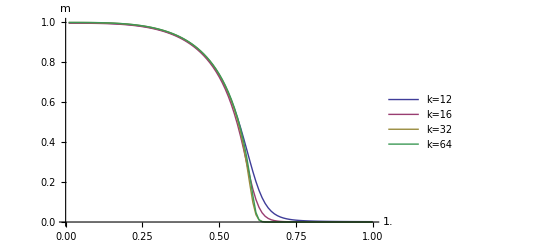

```mathematica
ListLinePlot[Table[Table[{μVector[[i]],Magμ1[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]
```

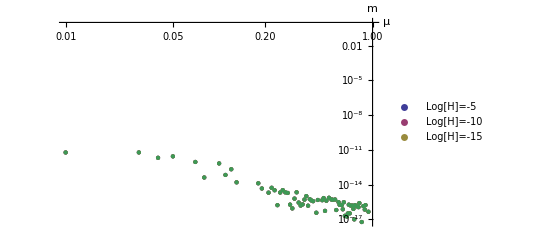

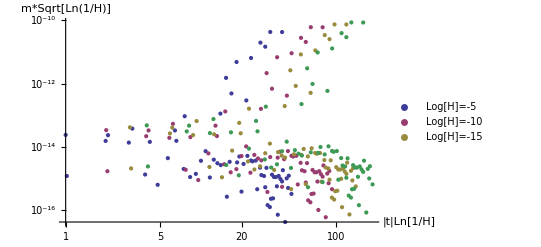

```mathematica
(***** Nogawa Plot 3: <m>(-Ln(H)) vs |t|(-Ln(H))*****)
Clear[μ,η,y];
y=0;
InitRGW;
μmin=N[0.01,200];
μmax=N[1.0,200];
μinc=N[0.01,200];
μVector=Range[μmin,μmax,μinc];
HVector={1/10^50, 1/10^100,1/10^150,1/10^200};
ηVector=Exp[-2*HVector];
kn=16;
MagH=ConstantArray[0,{Dimensions[HVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[hi=1,hi≤Dimensions[HVector][[1]],++hi,
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ,η];
kind=1;
InitRGW;
μ=μVector[[i]];
η=ηVector[[hi]];
For[j=3,j≤kn,++j
RGW;
];
Part[Part[MagH,hi],i]=1/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);
];
];
ListLogLogPlot[Table[Table[{μVector[[i]],MagH[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[HVector][[1]]}],PlotLegends->{"Log[H]=-5","Log[H]=-10","Log[H]=-15"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"μ","m"}]
ListLogLogPlot[Table[Table[{Abs[2*Sqrt[μVector[[i]]]-1]*(-Log10[HVector][[j]]),MagH[[j]][[i]]*Sqrt[-Log10[HVector][[j]]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[HVector][[1]]}],PlotLegends->{"Log[H]=-5","Log[H]=-10","Log[H]=-15"},PlotStyle->Thick,AxesLabel->{"|t|Ln[1/H]","m*Sqrt[Ln(1/H)]"}]
```

```mathematica
Rasterize[ListLogLogPlot[Table[Table[{Abs[2*Sqrt[μVector[[i]]]-1]*(-Log10[HVector][[j]]),MagH[[j]][[i]]*Sqrt[-Log10[HVector][[j]]]},{i,1,Dimensions[μVector][[1]]-20}],{j,1,Dimensions[HVector][[1]]}],PlotLegends->Placed[{"Log[H]=-50","Log[H]=-100","Log[H]=-150" ,"Log[H]=-200"},{Bottom,Left}],PlotStyle->Thick,AxesLabel->{"|t|Ln[1/H]","m*Sqrt[Ln(1/H)]"}]]
```

-Graphics-

-Graphics-

```mathematica
(****************************************** 2 Point Functions *********************************************)
```

```mathematica
Clear[μ,η,y]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->μ^y,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,5}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[D[(B[i]/.SBT),A[j]],{j,0,dim-1},{i,0,dim-1}];
Ω=Table[D[D[(B[i]/.SBT),A[j]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
InitRGW:=Block[{},InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];];
RGW:=Block[{},Υ=Together[Υ.(W/.SAT)];
RG;];
Ω=Table[D[D[(B[j]/.SBT),A[i]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}];
InitRGΩ:=Block[{},InitRGW;
Λ=0*Array[KroneckerDelta,{dim,dim,dim}];
(*Λ=Table[D[Υ,A[j]],{j,0,dim-1}];
This is all zero,anyway!*)];
RGΩ:=Block[{},Λ=Together[Together[Λ.Together[W/.SAT]]+Transpose[Together[(Υ.Together[Ω/.SAT]).Transpose[Υ]],{1,3,2}]];
RGW;];
D2LnZ1=Factor[Table[D[DLnZ1,A[i]],{i,0,dim-1}]];
```

```mathematica
(****** Specific Heat : Cv ******)
Clear[η,μ]
InitRGΩ
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ]
η=1;
sh[T_,kmax_]:=Block[{k,DZ1,DZ2,term1,term2,term0,term3},Clear[μ,η];
InitRGΩ;
y=0;
μ=N[Exp[-2/T],50];
η=1;
For[k=1,k<kmax,k++,RGΩ];
Print["RGΩ Done."];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=(dμdβ)^2*(d2A0dμ2.Υ).DlnZ;
term1=d2μdβ2*(dA0dμ.Υ).DlnZ;
term2=dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ);
term3=dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ);
Return[(term0+term1+term2+term3)/2^kmax];]
```

{0,0,0,0,(-1+y) y μ^(-2+y),0,0,0}

```mathematica
Clear[η,μ,y]
InitRGΩ;
y=0;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
η=1;
precN=1000;
Tmin=N[0.011,precN];
Tmax=N[12.0,precN];
Tinc=N[0.05,precN];
Tvector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=Exp[2/Tvector];
μinvVector=1.0/μVector;
kVector=Range[6,9,1];(*,13,14,15,16,17,18,19,20,32,64,100,128,200,256};*)
Cvμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
μind=0;
Do[
kind=1;
μind++;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=(dμdβ)^2*(d2A0dμ2.Υ).DlnZ;
term1=d2μdβ2*(dA0dμ.Υ).DlnZ;
term2=dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ);
term3=dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ);
Part[Part[Cvμ,kind],μind]=(term0+term1+term2+term3)/2^i;kind++,];
],
{Ti,Tmin,(Tmax+Tinc),Tinc}
];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]]
Cvμc=Cvμ;
PrependTo[Cvμc,Tvector];
PrependTo[Cvμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
Cvμc=Transpose[Cvμc];
Cvμc=PrependTo[Cvμc,kVector];
If[y==0,Export["./GoogleDrive/Research/AntiHN/Maca/data/HN3_AFM_Cv_test2.csv",Cvμc],Export["./GoogleDrive/Research/AntiHN/Maca/data/HN5_AFM_Cv_test2.csv",Cvμc]]
```

-Graphics-

./GoogleDrive/Research/AntiHN/Maca/data/HN3_AFM_Cv_test2.csv

./GoogleDrive/Research/AntiHN/Maca/data/HN3_AFM_Cv_test2.csv

./GoogleDrive/Research/AntiHN/Maca/data/HN3_AFM_Cv_test2.csv

Part::partw: Part 5 of {{-1.45217×10^-13, 3.80941×10^-8, 2.22045×10^-16, 0.0187185, 0.261703, 0.179784, 0.415729, 0.609475, 0.708405, « 34 », 1.42294, 1.44953, 1.47547, 1.50078, 1.52547, 1.54954, 1.57301, « 191 »}, « 2 », {« 1 »}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

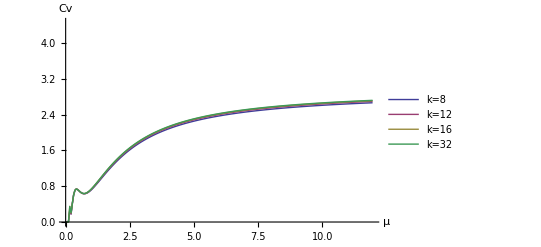

```mathematica
"./GoogleDrive/Research/AntiHN/Maca/data/HN3_AFM_Cv_test2.csv"
ListLinePlot[Table[Table[{Tvector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]
```

```mathematica
Clear[η,μ,y]
InitRGΩ;
y=0;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
η=1;
μinvmin=N[0.01,100];
μinvmax=N[1.0,100];
μinvinc=N[0.02,100];
μinvVector=Range[μinvmin,μinvmax,μinvinc];
μVector=1.0/μinvVector;
kVector={8,12,16,32}(*,64,128}*);
Cvμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
μind=0;
Do[
kind=1;
μind++;
InitRGΩ;
μ=μinvVector[[μind]];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=(dμdβ)^2*(d2A0dμ2.Υ).DlnZ;
term1=d2μdβ2*(dA0dμ.Υ).DlnZ;
term2=dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ);
term3=dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ);
Part[Part[Cvμ,kind],μind]=(term0+term1+term2+term3)/2^i;kind++,];
],
{μi,μinvmin,μinvmax,μinvinc}
];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]]
```

-Graphics-

```mathematica
μmin=N[0.01,100];
μmax=N[1.0,100];
μinc=N[0.01,100];
μVector=Range[μmin,μmax,μinc];
kVector={8,12,16,32}(*,64,128}*);
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","Cv"},AxesOrigin->{0,0},PlotRange->Full]]
```

-Graphics-

```mathematica
(******************* Susceptbility: χ *********************)
Clear[η,μ]
InitRGΩ
dηdH=-2 η
d2ηdH2=4 η
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}]
d2A0dη2=D[dA0dη,η]
Chi[T_,kmax_]:=Block[{k,DZ1,DZ2,term1,term2,term0,term3},Clear[μ,η,y];
InitRGΩ;
y=0;
Print["InitRGΩ!"];
μ=Exp[-4.0/T];
η=1;
For[k=1,k<kmax,k++,RGΩ;Print["k=",k]];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Return[(term0+term1+term2+term3)/2^kmax];]
```

```mathematica
Clear[η,μ,y];
InitRGΩ;
μmin=0.01;
μmax=1.0;
μinc=0.05;
μVector=Range[μmin,μmax,μinc];
kVector={8,10,12}(*,64,128}*);
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
```

```mathematica
Clear[η,μ,y];
InitRGΩ;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
kVector={8,12,16}(*,64,128}*);
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
```

```mathematica
y=1;
kind=1;
η=Exp[-2/10^2];
μind=0;
Do[
kind=1;
μind++;
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],
{μ,μmin,μmax,μinc}
];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
y=1;
kind=2;
η=Exp[-2/10^3];
μind=0;
Do[
μind++;
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],
{μ,μmin,μmax,μinc}
];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
y=1;
kind=3;
η=Exp[-2/10^4];
μind=0;
Do[
μind++;
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],
{μ,μmin,μmax,μinc}
];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
Rasterize[ListLogPlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->Placed[{"k=8","k=12","k=16","k=32"},{Bottom,Center}],PlotStyle->Thick,Joined->True,AxesLabel->{"μ","χ"}]]
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->Placed[{"k=8","k=12","k=16","k=32"},{Bottom,Center}],PlotStyle->Thick,PlotRange->Full,AxesLabel->{"μ","χ"}]]
```

-Graphics-

-Graphics-

```mathematica
(*********** AFM ************)
```

```mathematica
Clear[η,μ,y];
InitRGΩ;
μinvmin=0.01;
μinvmax=1.0;
μinvinc=0.02;
μinvVector=Range[μinvmin,μinvmax,μinvinc];
kVector={8,12,16}(*,64,128}*);
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμafm=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
```

```mathematica
y=1;
kind=1;
η=Exp[-2/10^2];
μind=0;
Do[
μind++;
μ=1/μinvVector[[μind]];
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμafm,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],
{μinv,μinvmin,μinvmax,μinvinc}
];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμafm[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
y=1;
kind=2;
η=Exp[-2/10^3];
μind=0;
Do[
μind++;
μ=1/μinvVector[[μind]];
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμafm,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],
{μinv,μinvmin,μinvmax,μinvinc}
];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμafm[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-